```mathematica
points={
{1000,0.112},{2000,0.404},{3000,0.812},{4000,1.456},{5000,2.166},{6000,3.099},{7000,4.342},{8000,5.483},{9000,7.111}, {10000,8.774},
{11000,10.312},{12000,13.099}
};
```

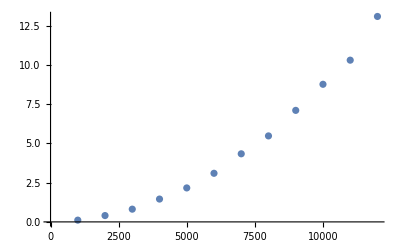

```mathematica
ListPlot@points
```

```mathematica
nlm=NonlinearModelFit[points,k x^2, {k}, {x}]
```

FittedModel[8.81093×10^-8 x^2]

```mathematica
results={};
Do[
primes={};
AppendTo[results,{k,AbsoluteTiming[
Do[
divisors=Length@Divisors[x];
AppendTo[primes,divisors]
,{x,k}]][[1]]}]
,
{k,Range[1000,12000,1000]}]
```

```mathematica
results
```

{{1000,0.014553},{2000,0.023972},{3000,0.038411},{4000,0.06829},{5000,0.080822},{6000,0.119934},{7000,0.147819},{8000,0.2098},{9000,0.241374},{10000,0.291024},{11000,0.329166},{12000,0.431857}}

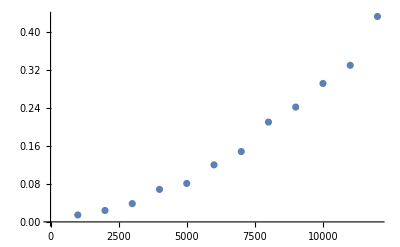

```mathematica
ListPlot@results
```

```mathematica
nlm=NonlinearModelFit[results,k x^2, {k}, {x}]
```

FittedModel[2.95219×10^-9 x^2]